```mathematica
mp=0.938272 1000;
mn=0.939565 1000;
μ=(mn+mp)/2;
sNN=62 1000;
```

```mathematica
y0[en_,m_]:=ArcTanh[(√(en^2-m^2))/en]
```

```mathematica
ρ[r_,θ_,R_,b_,θb_,pm_]:=2/(4/3 π R^3)√(R^2-(r^2+b^2/4+pm r b/2 Cos[θ-θb]))HeavisideTheta[R^2-(r^2+b^2/4+pm r b/2 Cos[θ-θb])];
```

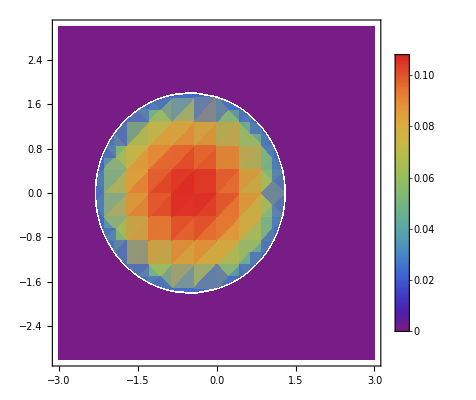

```mathematica
DensityPlot[Evaluate@TransformedField["Polar"->"Cartesian",ρ[r,θ,2,2,0,+1],{r,θ}->{x,y}],{x,-3,3},{y,-3,3},ColorFunction->"Rainbow",PlotLegends->Automatic](*centres at +/- b/2,pm gives different nucleus,R cut off*)
```

```mathematica
Integrate[r ρ[r,θ,R,0,0,+1],{r,0,∞},{θ,0,2π}]
```

ConditionalExpression[((R^2)^(3/2) HeavisideTheta[R^2])/R^3,Im[R]≠0]

```mathematica
τ[t_,z_]:=(t^2-z^2)^(1/2);
η[t_,z_]:=1/2 Log[(t+z)/(t-z)];
```

```mathematica
α=1/137;
Z=83;(*Pb*)
Z=79;
```

```mathematica
Bspec[r_,θ_,R_,b_,θb_,pm_,t_,z_,sNN_,m_]:=pm Z α Sinh[y0[sNN/2,m]+ pm η[t,z]]NIntegrate[r1 ρ[r1,θ1,R,b,θb,pm](1-HeavisideTheta[R^2-(r1^2+b^2/4-pm r1 b/2 Cos[θ1-θb])])Cross[{r1 Cos[θ1]-r Cos[θ],r1 Sin[θ1]-r Sin[θ],0},{0,0,1}]/((Norm[{r1 Cos[θ1]-r Cos[θ],r1 Sin[θ1]-r Sin[θ]}]^2+τ[t,z]^2 Sinh[y0[sNN/2,m]- pm η[t,z]]^2)^(3/2)),{r1,0,∞},{θ1,0,2π},MinRecursion->4,Method->"LocalAdaptive"]
```

```mathematica
Bspec[0,0,7/(0.197 1000),4/(0.197 1000) ,0,+1,1/(1000/5.06079),0,sNN,μ]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 14 recursive bisections in r1 near {r1,θ1} = {0.0324701,1.66899}. NIntegrate obtained 1.16303×10^-9 and 4.26631×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 14 recursive bisections in r1 near {r1,θ1} = {0.0324701,1.66902}. NIntegrate obtained 1.1631×10^-9 and 4.26656×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 14 recursive bisections in r1 near {r1,θ1} = {0.0324701,1.66904}. NIntegrate obtained 1.45089×10^-9 and 2.56658×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{-6.28878×10^-14,11.3924,0.}

```mathematica
Bspec[0,0,7/(0.197 1000),4/(0.197 1000) ,0,-1,1/(1000/5.06079),0,sNN,μ]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 14 recursive bisections in r1 near {r1,θ1} = {0.0285181,0.000283885}. NIntegrate obtained 1.21291×10^-12 and 3.08022×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 14 recursive bisections in r1 near {r1,θ1} = {0.0285181,0.000307854}. NIntegrate obtained 1.23635×10^-12 and 5.46624×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 14 recursive bisections in r1 near {r1,θ1} = {0.0285181,0.000331822}. NIntegrate obtained 1.33526×10^-12 and 5.90354×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{2.27254×10^-13,11.3924,0.}

```mathematica
a=0.5;
f[y_,en_,m_]:=a/(2 Sinh[a y0[en,m]])Exp[a y];
```

```mathematica
Bpart[r_,θ_,R_,b_,θb_,pm_,t_,z_,sNN_,m_]:=pm Z α NIntegrate[r1 f[y,sNN/2,m]Sinh[y- pm η[t,z]] ρ[r1,θ1,R,b,θb,pm]HeavisideTheta[R^2-(r1^2+b^2/4-pm r1 b/2 Cos[θ1-θb])] Cross[{r1 Cos[θ1]-r Cos[θ],r1 Sin[θ1]-r Sin[θ],0},{0,0,1}]/((Norm[{r1 Cos[θ1]-r Cos[θ],r1 Sin[θ1]-r Sin[θ]}]^2+τ[t,z]^2 Sinh[y0[sNN/2,m]- pm η[t,z]]^2)^(3/2)),{r1,0,∞},{θ1,0,2π},{y,-y0[sNN/2,m],y0[sNN/2,m]},MinRecursion->4,Method->"LocalAdaptive"];
```

```mathematica
Bpart[0,0,7/(0.197 1000),4/(0.197 1000),0,+1,1/(1000/5.06079),0,sNN,μ]//AbsoluteTiming
```

$Aborted